```mathematica
Remove["Global`*"]
```

```mathematica
SetDirectory["/users/home/arway/Desktop/Work/data/3dec16c/infldata"]
```

/users/home/arway/Desktop/Work/data/3dec16c/infldata

```mathematica
filenames=Sort[FileNames[DigitCharacter..~~"_infl.dat"],#1>#2&]
```

{10_infl.dat,11_infl.dat,12_infl.dat,13_infl.dat,14_infl.dat,15_infl.dat,16_infl.dat,17_infl.dat,18_infl.dat,19_infl.dat,1_infl.dat,20_infl.dat,21_infl.dat,22_infl.dat,23_infl.dat,24_infl.dat,25_infl.dat,26_infl.dat,27_infl.dat,28_infl.dat,29_infl.dat,2_infl.dat,30_infl.dat,31_infl.dat,32_infl.dat,33_infl.dat,34_infl.dat,35_infl.dat,36_infl.dat,37_infl.dat,38_infl.dat,39_infl.dat,3_infl.dat,40_infl.dat,41_infl.dat,42_infl.dat,43_infl.dat,44_infl.dat,45_infl.dat,46_infl.dat,47_infl.dat,4_infl.dat,5_infl.dat,6_infl.dat,7_infl.dat,8_infl.dat,9_infl.dat}

```mathematica
DATALIST=SortBy[filenames,ToExpression@FileBaseName[#]&]
```

{1_infl.dat,2_infl.dat,3_infl.dat,4_infl.dat,5_infl.dat,6_infl.dat,7_infl.dat,8_infl.dat,9_infl.dat,10_infl.dat,11_infl.dat,12_infl.dat,13_infl.dat,14_infl.dat,15_infl.dat,16_infl.dat,17_infl.dat,18_infl.dat,19_infl.dat,20_infl.dat,21_infl.dat,22_infl.dat,23_infl.dat,24_infl.dat,25_infl.dat,26_infl.dat,27_infl.dat,28_infl.dat,29_infl.dat,30_infl.dat,31_infl.dat,32_infl.dat,33_infl.dat,34_infl.dat,35_infl.dat,36_infl.dat,37_infl.dat,38_infl.dat,39_infl.dat,40_infl.dat,41_infl.dat,42_infl.dat,43_infl.dat,44_infl.dat,45_infl.dat,46_infl.dat,47_infl.dat}

```mathematica
Do[data[i]=Import[DATALIST[[i]]],{i,1,Length[DATALIST]}]
```

```mathematica
fieldData=Import["field_angles.dat","Table"];
```

Import::nffil: File not found during Import.

```mathematica
Bound[ϕ_]:=If[Cos[4 ϕ]==1,π/3,ArcSin[Sqrt[(4-Sqrt[16-6 (1-Cos[4 ϕ])])/(1-Cos[4 ϕ])]]]
```

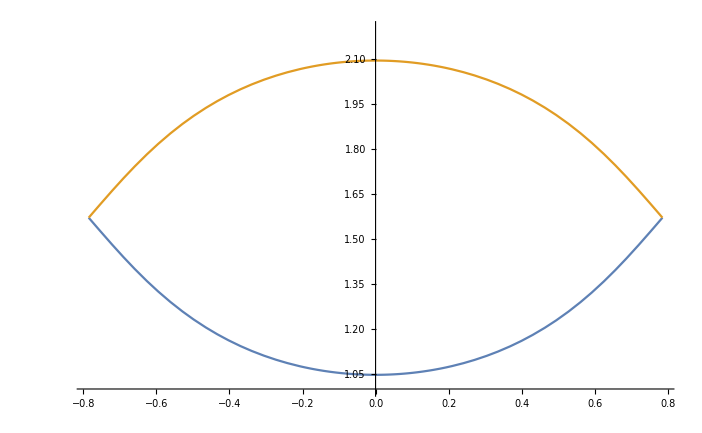

```mathematica
boundPlot=Plot[{Bound[ϕ],π-Bound[ϕ]},{ϕ,-π/4,π/4},PlotRange->{{-π/4,π/4},{1,2.2}}]
```

```mathematica
marker2=Graphics[{RGBColor[1,1,1],Disk[]}];
```

```mathematica
contour=Manipulate[Show[ListContourPlot[data[i],InterpolationOrder->1000,PlotLegends->Automatic,AxesLabel->{"Phi","Theta"}],boundPlot]
,{i,1,Length[DATALIST],1}]
```

ListContourPlot::arrayerr: data[1.] must be a valid array.

Show::gcomb: Could not combine the graphics objects in Show[ListContourPlot[data[1],InterpolationOrder→1000,PlotLegends→Automatic,AxesLabel→{Phi,Theta}],boundPlot].

ListContourPlot::arrayerr: data[1.] must be a valid array.

Show::gcomb: Could not combine the graphics objects in Show[ListContourPlot[data[1],InterpolationOrder→1000,PlotLegends→Automatic,AxesLabel→{Phi,Theta}],].

```mathematica
Export["highField111.avi",contour,"FrameRate"->30]
```

highField111.avi